# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["/Users/pcs/Desktop/Entropy/Calculations/Latest computation/t1 data/Equilibration time/L = 8/QMB.wl"];
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
```

# Teq

```mathematica
Clear[new];
new[ini_,t_,L_]:=Module[{schmidt,psit,ck=Conjugate[allvecs] . ini,d=2^(L/2)},
psit=ArrayReshape[N[Total[ ck * Exp[-I*allvals*t] * allvecs]],{d,d}];
schmidt=Total[Map[VNentropy,(Chop[SingularValueList[psit]])^2]]
];
```

```mathematica
L=8;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=1;
g=0.01;
h=1;
H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
La=L/2;
Lb=L-La;
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
```

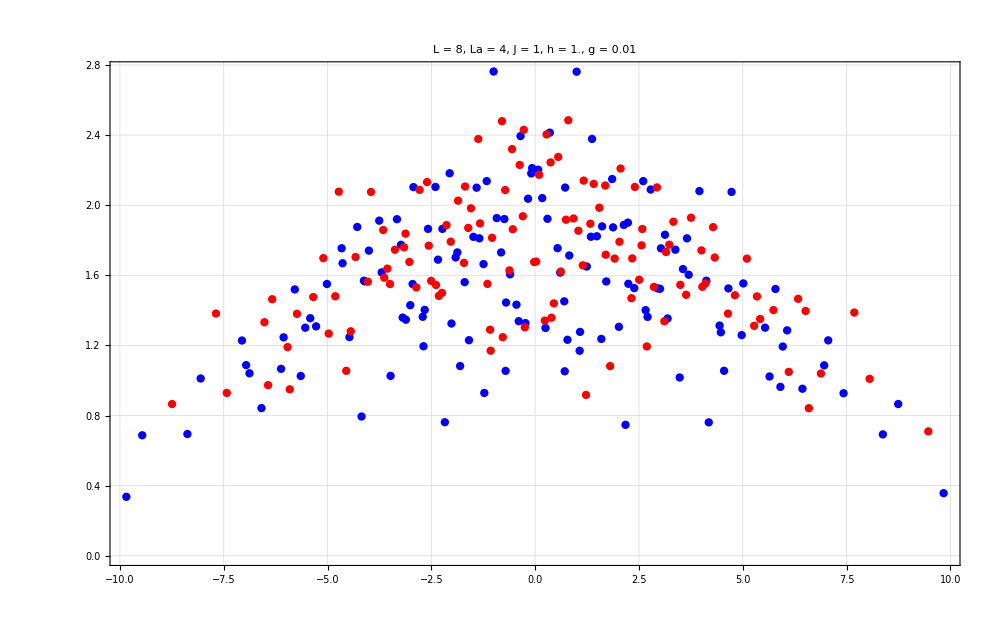

```mathematica
ListPlot[{Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Blue,PointSize[0.006]],Directive[Red,PointSize[0.006]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]]
```

## Half Haar

```mathematica
J=1;
g=0.01;
h=1;
H=IsingNNOpenHamiltonian[h,g,J,L];
{allvals,allvecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
allvecs=Orthogonalize[allvecs];
```

```mathematica
tlist=Table[i,{i,0,2000,0.1}];
tlist//Length
```

20001

```mathematica
allstates=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]],1],1000];
```

```mathematica
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstatesfull=data[[All,2]];
sortediprs=(data[[All,1]]);
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstatesfull},DistributedContexts->Full];
```

```mathematica
entropy2=ParallelTable[{t,new[j,t,L]},{j,productstatesfull},{t,tlist},DistributedContexts->Full,Method->"CoarsestGrained"];
```

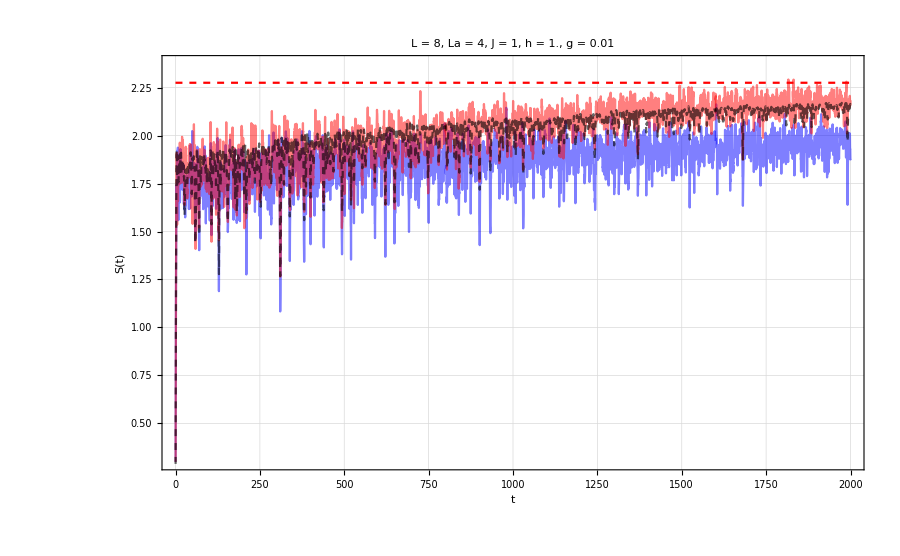

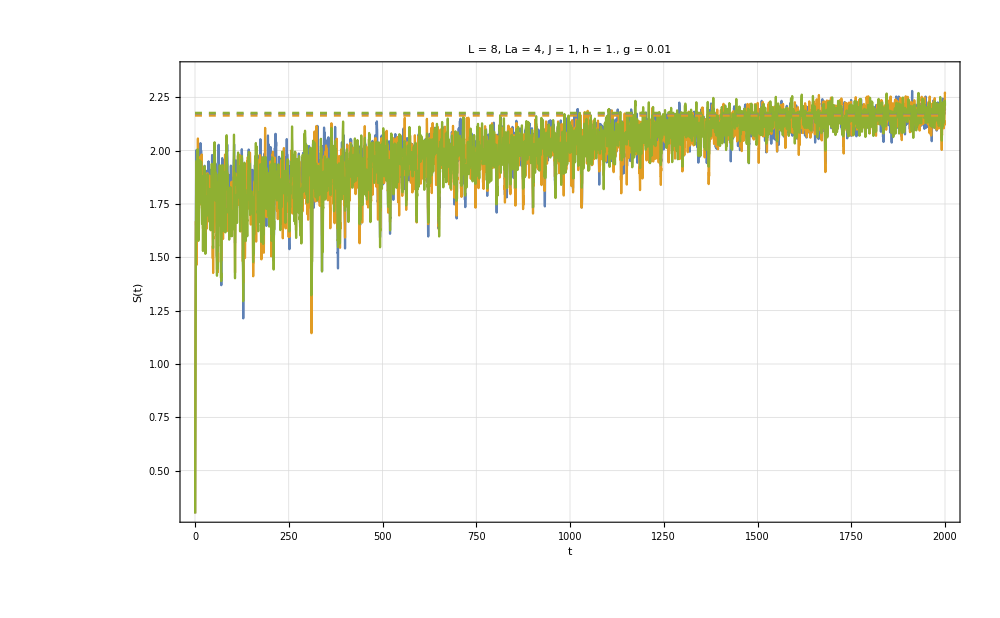

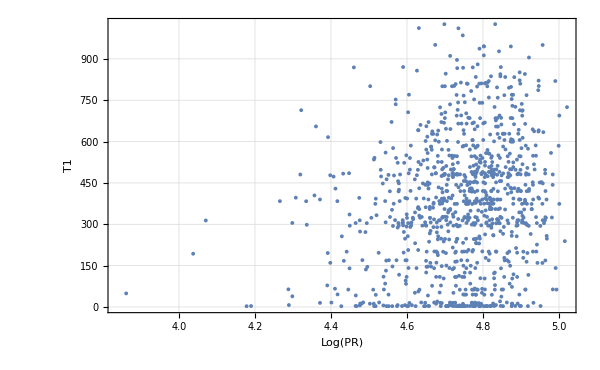

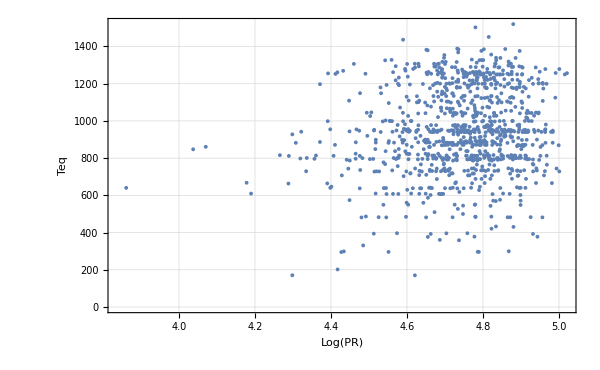

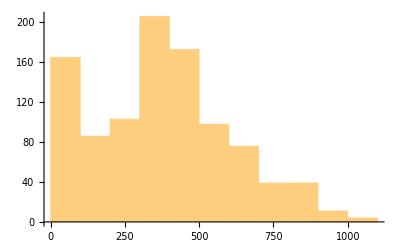

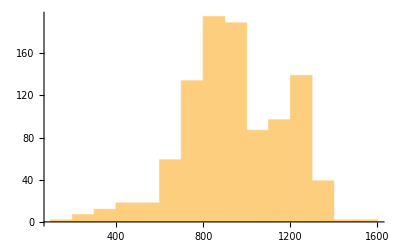

```mathematica
Show[{ListPlot[{entropy2[[1]],entropy2[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],ListPlot[Mean[entropy2],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
alldata={};
Do[
data=entropy2[[j]];
win=50;
mvAvg=MovingAverage[data[[All,2]],win];
timesMA=data[[win;;,1]];  
plateau=Mean[data[[All,2]][[-500;;-1]]];
tol=0.01*plateau;
pos=First@Flatten@Position[Abs[mvAvg-plateau],x_/;x<tol];
tSat=timesMA[[pos]];
index=FirstPosition[data[[All,2]]-plateau,x_/;x>0,None];
AppendTo[alldata,{plateau,tSat,tlist[[index[[1]]]]}];
,{j,Length[entropy2]}];
(*infofull=Transpose[{alldata[[All,2]],alldata[[All,3]],sortediprs,energies,alldata[[All,1]],entropy2}];*)
infofull=Transpose[{alldata[[All,3]],alldata[[All,2]],sortediprs,energies,alldata[[All,1]],entropy2}];
sortedinfofull=SortBy[infofull,First];
limits=sortedinfofull[[All,5]];
Show[{ListPlot[{sortedinfofull[[-3,6]],sortedinfofull[[-2,6]],sortedinfofull[[-1,6]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Half Haar ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],Plot[{limits[[-3]],limits[[-2]],limits[[-1]]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->Dashed]}]
ListPlot[Transpose[{Log[sortedinfofull[[All,3]]],sortedinfofull[[All,1]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["Log(PR)",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{Log[sortedinfofull[[All,3]]],sortedinfofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["Log(PR)",20,Black],Style["Teq",20,Black]},FrameStyle->Directive[Black,18]]

Histogram[sortedinfofull[[All,1]]]
Histogram[sortedinfofull[[All,2]]]
```

## RPS

```mathematica
J=1;
g=0.01;
h=1;
H=IsingNNOpenHamiltonian[h,g,J,L];
{allvals,allvecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
allvecs=Orthogonalize[allvecs];
```

```mathematica
tlist=Table[i,{i,0,2000,0.1}];
tlist//Length
```

20001

```mathematica
allstates=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstatesfull=data[[All,2]];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstatesfull},DistributedContexts->Full];
```

```mathematica
entropy2=ParallelTable[{t,new[j,t,L]},{j,productstatesfull},{t,tlist},DistributedContexts->Full,Method->"CoarsestGrained"];
```

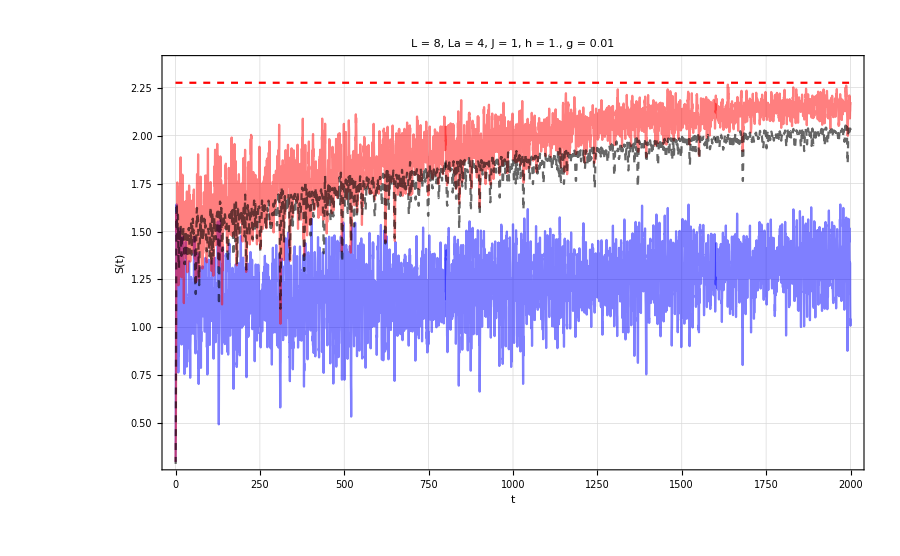

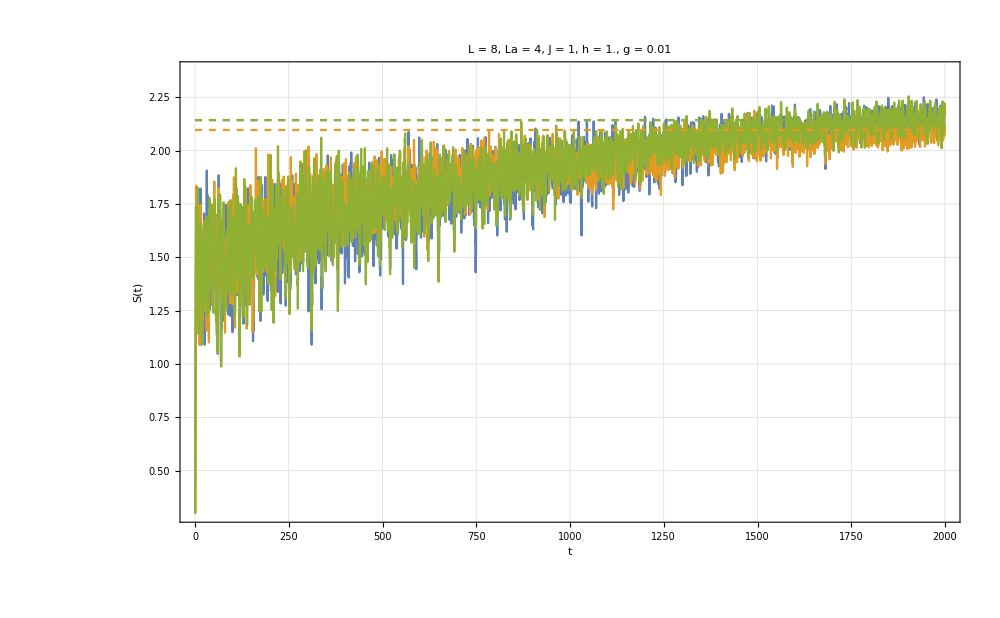

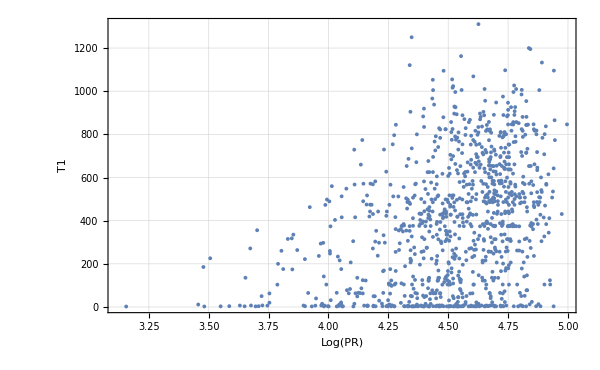

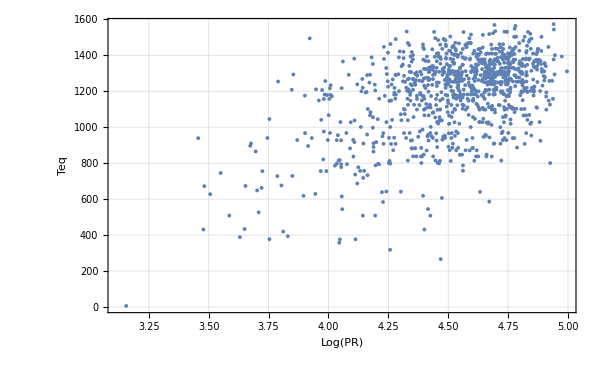

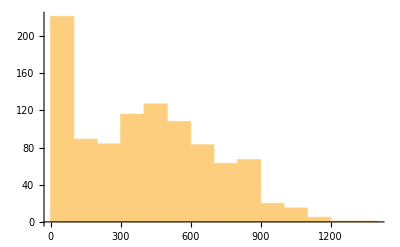

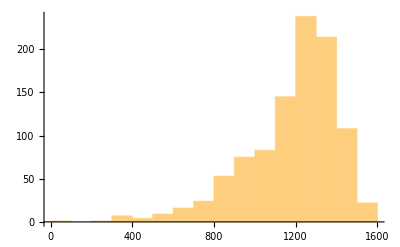

```mathematica
Show[{ListPlot[{entropy2[[1]],entropy2[[-1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,PlotStyle->{Directive[Blue,Opacity[0.5]],Directive[Red,Opacity[0.5]]},ImageSize->900,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],ListPlot[Mean[entropy2],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.2}},Joined->True,PlotStyle->Directive[Black,Opacity[0.6],Dashed],ImageSize->800,PlotTheme->"Detailed"],Plot[{pageEntropy[La,Lb]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Red,Dashed]}]}]
alldata={};
Do[
data=entropy2[[j]];
win=50;
mvAvg=MovingAverage[data[[All,2]],win];
timesMA=data[[win;;,1]];  
plateau=Mean[data[[All,2]][[-500;;-1]]];
tol=0.01*plateau;
pos=First@Flatten@Position[Abs[mvAvg-plateau],x_/;x<tol];
tSat=timesMA[[pos]];
index=FirstPosition[data[[All,2]]-plateau,x_/;x>0,None];
AppendTo[alldata,{plateau,tSat,tlist[[index[[1]]]]}];
,{j,Length[entropy2]}];
infofullrps=Transpose[{alldata[[All,3]],alldata[[All,2]],sortediprs,energies,alldata[[All,1]],entropy2}];
sortedinfofull=SortBy[infofullrps,First];
limits=sortedinfofull[[All,5]];
Show[{ListPlot[{sortedinfofull[[-3,6]],sortedinfofull[[-2,6]],sortedinfofull[[-1,6]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{0.3,pageEntropy[La,Lb]+0.1}},Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],PlotLegends->Style["Full RPS ",25,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],Plot[{limits[[-3]],limits[[-2]],limits[[-1]]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->Dashed]}]
ListPlot[Transpose[{Log[sortedinfofull[[All,3]]],sortedinfofull[[All,1]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["Log(PR)",20,Black],Style["T1",20,Black]},FrameStyle->Directive[Black,18]]
ListPlot[Transpose[{Log[sortedinfofull[[All,3]]],sortedinfofull[[All,2]]}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600,FrameLabel->{Style["Log(PR)",20,Black],Style["Teq",20,Black]},FrameStyle->Directive[Black,18]]

Histogram[sortedinfofull[[All,1]]]
Histogram[sortedinfofull[[All,2]]]
```

# Cycle

```mathematica
Clear[new];
new[ini_,t_,L_]:=Module[{schmidt,psit,ck=Conjugate[allvecs] . ini,d=2^(L/2)},
psit=ArrayReshape[N[Total[ ck * Exp[-I*allvals*t] * allvecs]],{d,d}];
schmidt=Total[Map[VNentropy,(Chop[SingularValueList[psit]])^2]]
];
```

## RPS

```mathematica
L=8;
La=L/2;
Lb=L-La;
J=1;
h=1;
tlist=Table[i,{i,0,2500,0.1}];
allstates=Table[RandomChainProductState[L],200];
```

```mathematica
glist=Table[10^i,{i,-2,0,0.01}];
```

```mathematica
allstates=Table[RandomChainProductState[L],200];
Do[

H=IsingNNOpenHamiltonian[h,g,J,L];
{allvals,allvecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
allvecs=Orthogonalize[allvecs];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstatesfull=data[[All,2]];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstatesfull},DistributedContexts->Full];
entropy2=ParallelTable[{t,new[j,t,L]},{j,productstatesfull},{t,tlist},DistributedContexts->Full,Method->"CoarsestGrained"];
alldata={};
Do[
data=entropy2[[j]];
win=50;
mvAvg=MovingAverage[data[[All,2]],win];
timesMA=data[[win;;,1]];  
plateau=Mean[data[[All,2]][[-500;;-1]]];
tol=0.01*plateau;
pos=First@Flatten@Position[Abs[mvAvg-plateau],x_/;x<tol];
tSat=timesMA[[pos]];
index=FirstPosition[data[[All,2]]-plateau,x_/;x>0,None];
AppendTo[alldata,{plateau,tSat,tlist[[index[[1]]]]}];
,{j,Length[entropy2]}];
infofullrps=Transpose[{alldata[[All,2]],alldata[[All,3]],sortediprs,energies,alldata[[All,1]]}];
Export["teq_t1_ipr_energy_saturation_L_"<>ToString[L]<>"_RPS_h_1_g_"<>ToString[g]<>"_.m",infofullrps];

,{g,glist}]
```

```mathematica
L=6;
allstates=Table[RandomChainProductState[L],200];
Do[

H=IsingNNOpenHamiltonian[h,g,J,L];
{allvals,allvecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
allvecs=Orthogonalize[allvecs];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstatesfull=data[[All,2]];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstatesfull},DistributedContexts->Full];
entropy2=ParallelTable[{t,new[j,t,L]},{j,productstatesfull},{t,tlist},DistributedContexts->Full,Method->"CoarsestGrained"];
alldata={};
Do[
data=entropy2[[j]];
win=50;
mvAvg=MovingAverage[data[[All,2]],win];
timesMA=data[[win;;,1]];  
plateau=Mean[data[[All,2]][[-500;;-1]]];
tol=0.01*plateau;
pos=First@Flatten@Position[Abs[mvAvg-plateau],x_/;x<tol];
tSat=timesMA[[pos]];
index=FirstPosition[data[[All,2]]-plateau,x_/;x>0,None];
AppendTo[alldata,{plateau,tSat,tlist[[index[[1]]]]}];
,{j,Length[entropy2]}];
infofullrps=Transpose[{alldata[[All,2]],alldata[[All,3]],sortediprs,energies,alldata[[All,1]]}];
Export["teq_t1_ipr_energy_saturation_L_"<>ToString[L]<>"_RPS_h_1_g_"<>ToString[g]<>"_.m",infofullrps];

,{g,glist}]
```

```mathematica
L=4;
allstates=Table[RandomChainProductState[L],200];
Do[

H=IsingNNOpenHamiltonian[h,g,J,L];
{allvals,allvecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
allvecs=Orthogonalize[allvecs];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstatesfull=data[[All,2]];
sortediprs=data[[All,1]];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstatesfull},DistributedContexts->Full];
entropy2=ParallelTable[{t,new[j,t,L]},{j,productstatesfull},{t,tlist},DistributedContexts->Full,Method->"CoarsestGrained"];
alldata={};
Do[
data=entropy2[[j]];
win=50;
mvAvg=MovingAverage[data[[All,2]],win];
timesMA=data[[win;;,1]];  
plateau=Mean[data[[All,2]][[-500;;-1]]];
tol=0.01*plateau;
pos=First@Flatten@Position[Abs[mvAvg-plateau],x_/;x<tol];
tSat=timesMA[[pos]];
index=FirstPosition[data[[All,2]]-plateau,x_/;x>0,None];
AppendTo[alldata,{plateau,tSat,tlist[[index[[1]]]]}];
,{j,Length[entropy2]}];
infofullrps=Transpose[{alldata[[All,2]],alldata[[All,3]],sortediprs,energies,alldata[[All,1]]}];
Export["teq_t1_ipr_energy_saturation_L_"<>ToString[L]<>"_RPS_h_1_g_"<>ToString[g]<>"_.m",infofullrps];

,{g,glist}]
```